# Exact continuum representation for long-range interacting systems: Phase diagram of exotic superconductors with long-range interactions

by Andreas A . Buchheit and Torsten Keßler

```mathematica
SetDirectory[NotebookDirectory[]];
```

Load MaTex Package. It can be installed by the command:

```mathematica
(*ResourceFunction["MaTeXInstall"][]*)
```

```mathematica
<<MaTeX`
```

## Data import

The following data was created using a high-performance C code. We acknowledge the support of NHR@FAU who granted us access to their supercomputer in order to  generate this data.

We use the following data format: 
1 : time,
2 : ν
3 : C0
4 : U0
5 : DeltaUpUp, s - wave projection (zero, for debugging)
6 : DeltaUpUp, p - wave projection 
7 : DeltaUpUp, d - wave projection (zero, for debugging)
8 : DeltaUpDown, s - wave projection 
9 : DeltaUpDown, p - wave projection
10 : DeltaUpDown, d - wave projection
11 : DeltaDownDown, s - wave projection (zero, for debugging)
12 : DeltaDownDown, p - wave projection 
13 : DeltaDownDown, d - wave projection (zero, for debugging)
14 : Energy
15 : Residuum of fixed point iteration
16 : Number of iteration until residuum reached 10^(-14)

We have generated a data array with 64 points in ν and 64 points in U0 .

Data for C0 = 0:

```mathematica
dataTriplet=ArrayReshape[Import["dataPhase/classification-triplet-64.dat","Real64"],{64*64,16}];
```

Data for C0 = 0.75, bias towards the s-wave phase.

```mathematica
dataC0=ArrayReshape[Import["dataPhase/classification-triplet-C0-64.dat","Real64"],{64*64,16}];
```

Due to bistability for C0=0.75 that arises at the first order transition, we compare energies and choose the solution with the lowest energy.

```mathematica
dataComplete=Table[If[dataC0[[i]][[14]]<dataTriplet[[i]][[14]],dataC0[[i]],dataTriplet[[i]]],{i,1,Length[dataC0]}];
```

## Generate phase boundaries

We generate the phase boundary between the d and d+p phase for C0=0.

```mathematica
dataNew=ArrayReshape[dataTriplet,{64,64,16}];
transitionTab={};
For[j=1,j<=64,j++,For[i=1,i<64,i++,If[dataNew[[j,i]][[6]]<10^(-11)&&dataNew[[j,i+1]][[6]]>10^(-11),AppendTo[transitionTab,{dataNew[[j,i]][[2]],dataNew[[j,i]][[4]]}];
AppendTo[transitionTab,{dataNew[[j,i+1]][[2]],dataNew[[j,i+1]][[4]]}]]]];
transitionTabTriplet=transitionTab;
```

We generate the phase boundary between s and d+s.

```mathematica
dataNew=ArrayReshape[dataComplete,{64,64,16}];
transitionTab={};
For[j=1,j<=64,j++,For[i=1,i<64,i++,If[dataNew[[j,i]][[10]]<10^(-11)&&dataNew[[j,i+1]][[10]]>10^(-11),AppendTo[transitionTab,{dataNew[[j,i]][[2]],dataNew[[j,i]][[4]]}];
AppendTo[transitionTab,{dataNew[[j,i+1]][[2]],dataNew[[j,i+1]][[4]]}]]]];
transitionTabS=transitionTab;
```

Phase boundary between d+s and d+p.

```mathematica
dataNew=ArrayReshape[dataComplete,{64,64,16}];
transitionTab={};
For[j=1,j<=64,j++,For[i=1,i<64,i++,If[dataNew[[j,i]][[8]]>10^(-11)&&dataNew[[j,i+1]][[8]]<10^(-11)&&dataNew[[j,i+1]][[6]]>10^(-11),AppendTo[transitionTab,{dataNew[[j,i]][[2]],dataNew[[j,i]][[4]]}];
AppendTo[transitionTab,{dataNew[[j,i+1]][[2]],dataNew[[j,i+1]][[4]]}]]]];
transitionTabSDToPD=transitionTab;
```

Phase boundary between d+s and the d-wave phase.

```mathematica
dataNew=ArrayReshape[dataComplete,{64,64,16}];
transitionTab={};
For[j=1,j<=64,j++,For[i=1,i<64,i++,If[dataNew[[j,i]][[8]]>10^(-11)&&dataNew[[j,i+1]][[8]]<10^(-11)&&dataNew[[j,i+1]][[6]]<10^(-11),AppendTo[transitionTab,{dataNew[[j,i]][[2]],dataNew[[j,i]][[4]]}];
AppendTo[transitionTab,{dataNew[[j,i+1]][[2]],dataNew[[j,i+1]][[4]]}]]]];
transitionTabSDToD=transitionTab;
```

We finally obtain the intervals in which the phase boundary is positioned.

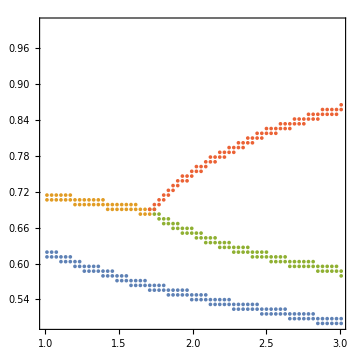

```mathematica
pS=ListPlot[{transitionTabS,transitionTabSDToPD,transitionTabSDToD,Drop[transitionTabTriplet,31]},PlotRange->{{1,3},{0.5,1}},Frame->True,ImageSize->Medium,AspectRatio->1,PlotTheme->"Detailed",BaseStyle->{FontFamily->"Latin Modern Roman"},FrameLabel->{MaTeX["\\nu",Magnification->1.3],MaTeX["U_0",Magnification->1.3]},PlotLegends->None,FrameStyle->Black,GridLines->None,LabelStyle->{FontSize->Scaled[.035],FontFamily->"Helvetica"}]
```

## Polynomial Fit to the phase boundaries

Subsequently, we find the best polynomial approximation to the phase boundaries. To this end, we use second order polynomials for C0 = 0.75 and for the larger phase boundary for C0 = 0 a fourth order polynomial fit.

```mathematica
model=off+a*x+b*x^2;
```

```mathematica
model4=off+a*x+b*x^2+c*x^3+d*x^4;
```

```mathematica
FitS[x_]=model/.Quiet[FindFit[transitionTabS,model,{off,a,b},x,Method->NMinimize]];
FitSDToPD[x_]=model/.Quiet[FindFit[transitionTabSDToPD,model,{off,a,b},x,Method->NMinimize]];
FitSDToD[x_]=model/.Quiet[FindFit[transitionTabSDToD,model,{off,a,b},x,Method->NMinimize]];
FitTriplet[x_]=model4/.Quiet[FindFit[transitionTabTriplet,model4,{off,a,b,c,d},x,Method->"NMinimize"]];
```

## Plot phase boundaries

We now generate the phase boundaries. In order not to fit a smooth curve at the triple point, we use separate fits for the respective phase boundaries.

```mathematica
νCrit=1.702;
```

```mathematica
pFitS=Plot[FitS[x],{x,1,3}];
```

```mathematica
pFitSDToPD=Plot[FitSDToPD[x],{x,1,νCrit}];
pFitSDToD=Plot[FitSDToD[x],{x,νCrit,3}];
pFitDToPD=Plot[FitTriplet[x],{x,νCrit,3}];
```

```mathematica
PhaseBoundaryP[x_]=If[x<νCrit,FitSDToPD[x],FitTriplet[x]];
```

```mathematica
PhaseBoundaryD[x_]=If[x<νCrit,FitSDToPD[x],FitSDToD[x]];
```

```mathematica
PhaseBoundaryS[x_]=FitS[x];
```

We obtain the following result for the phase boundaries. The polynomial fits reproduce the intervals very well.

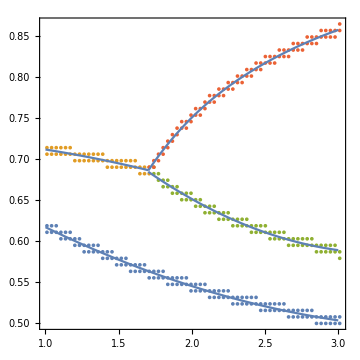

```mathematica
Show[pS,pFitSDToPD,pFitS,pFitSDToD,pFitDToPD,PlotRange->All,Frame->True,AspectRatio->1]
```

Finally, we generate the phase boundary between the d and p+d phase in case that C0 = 0,

```mathematica
pTriplet=Plot[FitTriplet[x],{x,1.0,3.0},PlotStyle->{Dashed,Black}];
```

and subsequently display the full Phase diagram.

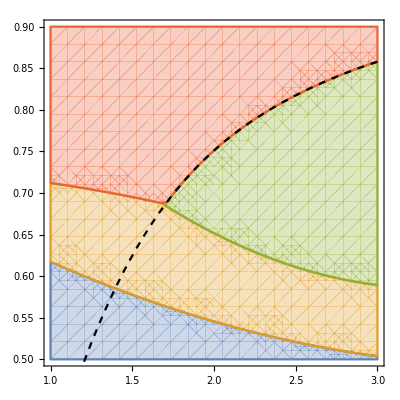

```mathematica
pPhases=Show[RegionPlot[{y<FitS[x],y>FitS[x]&&y<PhaseBoundaryD[x],y<PhaseBoundaryP[x]&&y>PhaseBoundaryD[x],y>PhaseBoundaryP[x]},{x,1,3},{y,0.5,.9},PlotTheme->"Detailed",BaseStyle->{FontFamily->"Latin Modern Roman"},FrameLabel->{MaTeX["\\nu",Magnification->1.3],MaTeX["U_0",Magnification->1.3]},PlotLegends->None,FrameStyle->Black,GridLines->None,LabelStyle->{FontSize->Scaled[.035],FontFamily->"Helvetica"},Epilog->{Text[MaTeX["\\text{s-wave}",Magnification->1.3],Scaled[{0.3,0.1}],{0,0}],Text[MaTeX["\\text{s+d-wave}",Magnification->1.3],Scaled[{0.5,0.24}],{0,0}],Text[MaTeX["\\text{nodal d-wave}",Magnification->1.3],Scaled[{0.7,0.5}],{0,0}],Text[MaTeX["\\text{chiral p+d-wave}",Magnification->1.3],Scaled[{0.4,0.8}],{0,0}]}],pTriplet]
```

```mathematica
(*Export["fig5.png",pPhases,ImageResolution->600];*)
```